```mathematica
pic=ImageData[-Graphics-]⟦All,All,1⟧;
```

```mathematica
dir={{0,1},{1,0},{0,-1},{-1,0}};(*This loop searches for the first edge to work around*)For[x=2;s={};xs=0;ys=0;n=0,x<480,x++,
For[y=2,y<640,y++,
If[pic⟦x,y⟧≠0&&Max[{pic⟦x+1,y+1⟧,pic⟦x+1,y⟧,pic⟦x+1,y-1⟧,pic⟦x,y-1⟧,pic⟦x-1,y-1⟧,pic⟦x-1,y⟧,pic⟦x-1,y+1⟧,pic⟦x,y+1⟧}]≠ 0,
xs=x;ys=y;x=480;y=640;s=Append[s,{n,xs,ys,pic⟦xs,ys⟧}]]]];
{xs,ys}
(*we consider 4 different directions, we always try to turn left if possible, think working through a maze with left hand on a wall*)
If[pic⟦xs+dir⟦1,1⟧,ys+dir⟦1,2⟧⟧≠0,xc=xs+dir⟦1,1⟧;yc=ys+dir⟦1,2⟧;ds=1;d=1,If[pic⟦xs+dir⟦2,1⟧,ys+dir⟦2,2⟧⟧≠0,xc=xs+dir⟦2,1⟧;yc=ys+dir⟦2,2⟧;ds=2;d=2]];
n++;
While[xc≠ xs||yc≠ ys,s=Append[s,{n,xc,yc ,pic⟦xc,yc⟧}];  If[pic⟦xc+dir⟦Mod[d-1,4,1],1⟧,yc+dir⟦Mod[d-1,4,1],2⟧⟧≠0,xc=xc+dir⟦Mod[d-1,4,1],1⟧;yc=yc+dir⟦Mod[d-1,4,1],2⟧;d=Mod[d-1,4,1],
If[pic⟦xc+dir⟦Mod[d,4,1],1⟧,yc+dir⟦Mod[d,4,1],2⟧⟧≠0,xc=xc+dir⟦Mod[d,4,1],1⟧;yc=yc+dir⟦Mod[d,4,1],2⟧;d=Mod[d,4,1],
If[pic⟦xc+dir⟦Mod[d+1,4,1],1⟧,yc+dir⟦Mod[d+1,4,1],2⟧⟧≠0,xc=xc+dir⟦Mod[d+1,4,1],1⟧;yc=yc+dir⟦Mod[d+1,4,1],2⟧;d=Mod[d+1,4,1],
If[pic⟦xc+dir⟦Mod[d+2,4,1],1⟧,yc+dir⟦Mod[d+2,4,1],2⟧⟧≠0,xc=xc+dir⟦Mod[d+2,4,1],1⟧;yc=yc+dir⟦Mod[d+2,4,1],2⟧;d=Mod[d+2,4,1]]]]];n++]
```

{33,305}

```mathematica
s⟦1⟧
```

{0,33,305,0.360784}

```mathematica
se[1]⟦1⟧
```

{0,33,305,0.360784}

```mathematica
Length[se[1]]
```

141

```mathematica
Length[se[2]]
```

141

```mathematica
Sum[se[i],{i,1,0}]
```

0

```mathematica
Round[3.2]
```

3

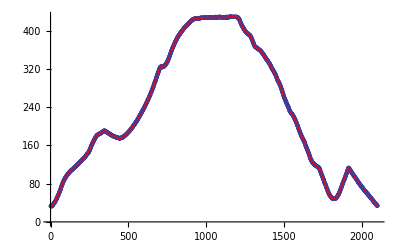

```mathematica
segments=105;Table[α[j,2]+β[j,2] ((j-1)*(Length[s]+1)/segments)+γ[j,2] ((j-1)*(Length[s]+1)/segments)^2-α[Round[Mod[j-1,segments,1]],2]-β[Round[Mod[j-1,segments,1]],2] ((j-1)*(Length[s]+1)/segments)-γ[Round[Mod[j-1,segments,1]],2] ((j-1)*(Length[s]+1)/segments)^2==0,{j,1,segments}];
Table[β[j,2]+2 γ[j,2] ((j-1)*(Length[s]+1)/segments)-β[Round[Mod[j-1,segments,1]],2] -2γ[Round[Mod[j-1,segments,1]],2] ((j-1)*(Length[s]+1)/segments)==0,{j,1,segments}];
Table[
Sum[α[j,2]+β[j,2] s⟦k,1⟧+γ[j,2] s⟦k,1⟧^2-s⟦k,2⟧,{k,Round[((j-1)*(Length[s])/segments)]+1,Round[((j)*(Length[s])/segments)]}]==0,{j,1,segments}];
NSolve[Join[%%%,%%,%],Flatten[Table[{α[j,2],β[j,2],γ[j,2]},{j,1,segments}]]]⟦1⟧;
Piecewise[Table[{α[j,2]+β[j,2] X+γ[j,2] X^2,X≥(j-1)*(Length[s])/segments&& X<j*(Length[s])/segments},{j,1,segments}]]/.%;
Show[ListPlot[s⟦All,2⟧],Plot[%,{X,0,len},PlotStyle->Red]]
```

```mathematica
len/segments
```

525.5

```mathematica
Piecewise[Table[{α[j,2]+β[j,2] X+γ[j,2] X^2,X≥(j-1)*(Length[s])/segments&& X<j*(Length[s])/segments},{j,1,segments}]]
```

Piecewise[{{α[1,2]+X β[1,2]+X^2 γ[1,2], X≥0.&&X<525.5}, {α[2,2]+X β[2,2]+X^2 γ[2,2], X≥525.5&&X<1051.}, {α[3,2]+X β[3,2]+X^2 γ[3,2], X≥1051.&&X<1576.5}, {α[4,2]+X β[4,2]+X^2 γ[4,2], X≥1576.5&&X<2102.}, {0, True}}]

```mathematica
s⟦Length[s]⟧
```

{2101,34,305,0.364706}

```mathematica
Table[
Sum[α[j,2]+β[j,2] s⟦k,1⟧+γ[j,2] s⟦k,1⟧^2-s⟦k,2⟧,{k,Round[((j-1)*(Length[s])/segments)]+1,Round[((j)*(Length[s])/segments)]}]==0,{j,1,segments}]
```

{-74000+526 α[1,2]+138075 β[1,2]+48372275 γ[1,2]==0,-182218+525 α[2,2]+413700 β[2,2]+338054150 γ[2,2]==0,-187897+525 α[3,2]+689325 β[3,2]+917142275 γ[3,2]==0,-50408+526 α[4,2]+967051 β[4,2]+1790050851 γ[4,2]==0}

```mathematica
j=1;
Table[α[j,2]+β[j,2] X+γ[j,2] s⟦k,1⟧^2 X^2,{k,Round[((j-1)*(Length[s])/segments)]+1,Round[((j)*(Length[s])/segments)]}];
%⟦Length[%]⟧
j=2;
Table[s⟦k⟧,{k,Round[((j-1)*(Length[s])/segments)]+1,Round[((j)*(Length[s])/segments)]}];
%⟦1⟧
j=1;
Table[s⟦k⟧,{k,Round[((j-1)*(Length[s])/segments)]+1,Round[((j)*(Length[s])/segments)]}];
%⟦1⟧
j=segments;
Table[s⟦k⟧,{k,Round[((j-1)*(Length[s])/segments)]+1,Round[((j)*(Length[s])/segments)]}];
%⟦Length[%]⟧
```

{525,198,423,0.537255}

{526,198,424,0.529412}

{0,33,305,0.360784}

{2101,34,305,0.364706}

```mathematica
Piecewise[Table[{α[j,2]+β[j,2] X+γ[j,2] X^2,X≥(j-1)*(Length[s])/segments&& X<j*(Length[s])/segments},{j,1,segments}]]
```

Piecewise[{{α[1,2]+X β[1,2]+X^2 γ[1,2], X≥0.&&X<525.5}, {α[2,2]+X β[2,2]+X^2 γ[2,2], X≥525.5&&X<1051.}, {α[3,2]+X β[3,2]+X^2 γ[3,2], X≥1051.&&X<1576.5}, {α[4,2]+X β[4,2]+X^2 γ[4,2], X≥1576.5&&X<2102.}, {0, True}}]

```mathematica
s⟦1⟧
```

{0,33,305,0.360784}

```mathematica
s⟦Length[s]⟧
```

{2101,34,305,0.364706}

```mathematica
segments=4.;
QuotientRemainder[len,segments]
Table[{1,%⟦1⟧+Sum[
```

{525,2.}

```mathematica
Length
```

```mathematica
For[j=1,j≤segments,j++,
se[j]=Table[s⟦Round[(Length[s]-Sum[se[i],{i,1,j-1}] )/segments]+k{k,1,Round[(Length[s]-Sum[se[i],{i,1,j-1}] )/segments]}]
```

```mathematica
{se[1]⟦Length[se[1]]⟧,se[2]⟦1⟧}
{se[2]⟦Length[se[2]]⟧,se[3]⟦1⟧}
```

{{140,110,298,0.439216},{141,110,297,0.443137}}

{{281,173,236,0.541176},{280,172,236,0.541176}}

```mathematica
segments=15;
QuotientRemainder[len,segments]
For[j=0,j<segments,j++,
se[j+1]=Table[s⟦(%⟦1⟧+If[j<%⟦2⟧,1,0])*j+i⟧,{i,1,%⟦1⟧+If[j<%⟦2⟧,1,0]}]];
```

{140,2.}

{140,2.}

{{49.3652+0.243698 X+0.000911004 X^2,X≥0&&X≤140},{28.6866+0.540165 X-0.000151603 X^2,X≥140&&X≤280},{-152.31+1.83531 X-0.00246851 X^2,X≥280&&X≤419},{856.244-2.97305 X+0.00326256 X^2,X≥420&&X≤559},{-149.96+0.623747 X+0.0000482632 X^2,X≥560&&X≤699},{-468.173+1.53358 X-0.000602079 X^2,X≥700&&X≤839},{-1469.56+3.91926 X-0.00202297 X^2,X≥840&&X≤979},{842.778-0.802214 X+0.000387171 X^2,X≥980&&X≤1119},{-2100.93+4.45675 X-0.00196163 X^2,X≥1120&&X≤1259},{750.5-0.0711214 X-0.000164142 X^2,X≥1260&&X≤1399},{-611.629+1.87547 X-0.000859603 X^2,X≥1400&&X≤1539},{731.636+0.130405 X-0.000292839 X^2,X≥1540&&X≤1679},{12143.6-13.4594 X+0.00375294 X^2,X≥1680&&X≤1819},{-5145.35+5.54475 X-0.00146941 X^2,X≥1820&&X≤1959},{49.3649+0.24267 X-0.000116489 X^2,X≥1960&&X≤2099}}

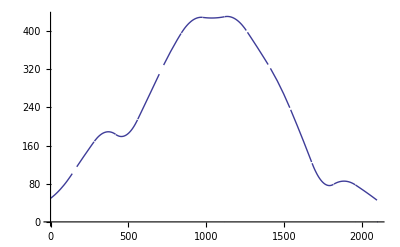

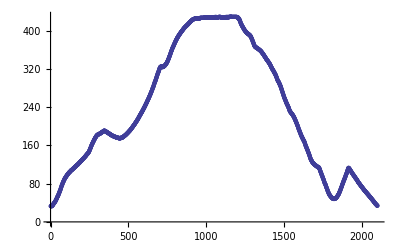

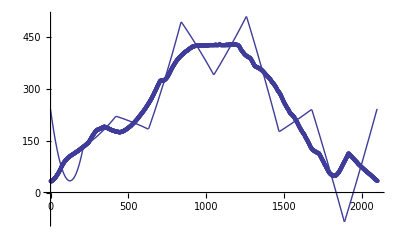

```mathematica
For[j=0,j<segments,j++,
se[j+1]=Table[s⟦(%⟦1⟧*j)+i⟧,{i,1,%⟦1⟧+If[j<%⟦2⟧,1,0]}]];
Table[α[j,2]+β[j,2](se[j]⟦1,1⟧-0.5)+γ[j,2](se[j]⟦1,1⟧-0.5)^2
-α[Mod[j-1,segments,1],2]-β[Mod[j-1,segments,1],2](se[j]⟦1,1⟧-0.5)-γ[Mod[j-1,segments,1],2](se[j]⟦1,1⟧-0.5)^2 ,{j,1,segments}];
Table[β[j,2]+2γ[j,2](se[j]⟦1,1⟧-0.5)
-β[Mod[j-1,segments,1],2]-2γ[Mod[j-1,segments,1],2](se[j]⟦1,1⟧-0.5) ,{j,1,segments}];
Table[Sum[α[j,2]+β[j,2]se[j]⟦i,1⟧+γ[j,2](se[j]⟦i,1⟧)^2 - se[j]⟦i,2⟧,{i,1,Length[se[j]]}],{j,1,segments}];
qq=Join[Table[%%%⟦i⟧==0,{i,1,Length[%%%]}],Table[%%⟦i⟧==0,{i,1,Length[%%]}],Table[%⟦i⟧==0,{i,1,Length[%]}]];
Table[{α[j,2]+β[j,2] X+γ[j,2] X^2,X≥ se[j]⟦1,1⟧&&X≤se[j]⟦Length[se[j]],1⟧},{j,1,segments}]/.Solve[qq,Flatten[Table[{α[j,2],β[j,2],γ[j,2]},{j,1,segments}]]]⟦1⟧
Plot[Piecewise[%],{X,0,Length[s]}]
ListPlot[s⟦All,2⟧]
```

```mathematica
Solve[qq,Flatten[Table[{α[j,2],β[j,2],γ[j,2]},{j,1,segments}]]]
```

{{α[1,2]→151.212,β[1,2]→0.0778396,γ[1,2]→-0.000632575,α[2,2]→316.462,β[2,2]→-0.000851798,γ[2,2]→-0.000115407,α[3,2]→354.006,β[3,2]→-0.00035574,γ[3,2]→0.000061818,α[4,2]→194.079,β[4,2]→0.0000459971,γ[4,2]→0.0000386782,α[5,2]→110.679,β[5,2]→0.0000956658,γ[5,2]→-9.14097×10^-6}}

```mathematica
Mod[j,4,1]
```

1

```mathematica
Table[Sum[α[j,2]+β[j,2]se[j]⟦i,1⟧+γ[j,2](se[j]⟦i,1⟧)^2 - se[j]⟦i,2⟧,{i,1,Length[se[j]]}],{j,1,segments}]
```

{-54864+421 α[1,2]+88410 β[1,2]+24784270 γ[1,2],-113003+421 α[2,2]+265230 β[2,2]+173313070 γ[2,2],-177505+420 α[3,2]+440790 β[3,2]+468783070 γ[3,2],-116860+420 α[4,2]+617190 β[4,2]+913134670 γ[4,2],-32798+420 α[5,2]+793590 β[5,2]+1505662270 γ[5,2]}

```mathematica
se[1]⟦Length[se[1]]⟧
```

{525,198,423,0.537255}

```mathematica
For[j=0,j<segments,j++,
α[j],β[j],γ[j]
```

```mathematica
se
```

```mathematica
α[j]+β[j] se[j]⟦i,1⟧ + γ[j](j-1)-se[j]⟦i,1⟧
```

```mathematica
Length[se[4]]
```

525

```mathematica
,
```

```mathematica
dat
```

{{{0.,0.,0.},{235.263,281.275,0.452208}},{{12.0315,146.322,0.0441394},{-183.36,-43.8925,-0.029262}},{{22.846,-59.8309,0.0426533},{22.5252,18.8213,-0.0591576}},{{8.31885,6.13819,0.0207919},{-0.508439,36.7306,0.019769}},{{-10.3207,-1.0357,-0.0200216},{-11.9779,6.56629,0.0131431}},{{-10.4761,17.2342,-0.0314019},{-5.04021,10.554,0.0195686}},{{-2.72377,6.38665,-0.0342203},{-5.62772,1.93524,-0.0212159}},{{1.35375,3.92457,-0.0126359},{-3.4587,-4.83654,-0.0196701}},{{4.77962,2.67669,0.00445655},{-7.54651,4.26245,-0.0264224}},{{3.89443,-1.85727,0.00919803},{-2.4441,-4.62945,-0.00221578}},{{1.43899,1.99913,0.00952088},{-1.44533,-0.271352,-0.00655767}},{{0.127008,-2.27749,-0.000182109},{0.0306344,3.03714,0.012898}},{{-2.36152,-0.026776,-0.0034988},{2.81486,-2.83636,-0.000500876}},{{-1.96932,-0.093639,-0.00161198},{0.385307,0.645341,0.00482531}},{{-2.14987,1.21213,-0.00420396},{-1.58238,-1.38243,0.000319443}},{{-0.947152,2.64912,-0.00254676},{-1.37532,-1.17559,0.00982681}}}

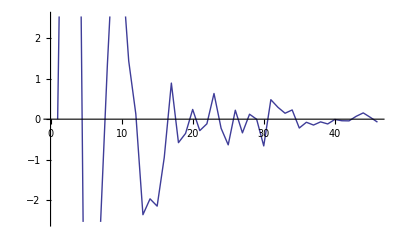

```mathematica
ListLinePlot[dat⟦All,1,1⟧]
```

```mathematica
jmax=15;dat=Table[(2 If[j==0,0.5,1])/len Sum[KroneckerProduct[{Sin[(2π j X)/len],Cos[(2π j X)/len]},s⟦X⟧],{X,1,len}],{j,0,jmax}];
Sum[%⟦j,1⟧ Sin[2π (j-1) X]+%⟦j,2⟧ Cos[2π(j-1) X],{j,1,jmax+1}];
Show[ListPointPlot3D[Table[%,{X,0,1,1/200}],PlotStyle->Red],ListPointPlot3D[s]]
```

-Graphics3D-

```mathematica
Sum[dat⟦j,1⟧ Sin[2π (j-1) X]+dat⟦j,2⟧ Cos[2π(j-1) X],{j,1,jmax+1}];
FindRoot[(%⟦1⟧-300)^2+(%⟦2⟧-300Λ)^2,
```

```mathematica
Sum[dat⟦j,1⟧ Sin[2π (j-1) X]+dat⟦j,2⟧ Cos[2π(j-1) X],{j,1,jmax+1}];
FindMinimum[(%⟦1⟧-300)^2,{X,0.5,0,1}]
```

{16206.8,{X→0.518934}}

```mathematica
Sum[dat⟦j,1⟧ Sin[2π (j-1) X]+dat⟦j,2⟧ Cos[2π(j-1) X],{j,1,jmax+1}];
FindRoot[%⟦1⟧==200,{X,5}]
```

{235.263-183.36 Cos[2 π X]+22.5252 Cos[4 π X]-0.508439 Cos[6 π X]-11.9779 Cos[8 π X]-5.04021 Cos[10 π X]-5.62772 Cos[12 π X]-3.4587 Cos[14 π X]-7.54651 Cos[16 π X]-2.4441 Cos[18 π X]-1.44533 Cos[20 π X]+0.0306344 Cos[22 π X]+2.81486 Cos[24 π X]+0.385307 Cos[26 π X]-1.58238 Cos[28 π X]-1.37532 Cos[30 π X]+12.0315 Sin[2 π X]+22.846 Sin[4 π X]+8.31885 Sin[6 π X]-10.3207 Sin[8 π X]-10.4761 Sin[10 π X]-2.72377 Sin[12 π X]+1.35375 Sin[14 π X]+4.77962 Sin[16 π X]+3.89443 Sin[18 π X]+1.43899 Sin[20 π X]+0.127008 Sin[22 π X]-2.36152 Sin[24 π X]-1.96932 Sin[26 π X]-2.14987 Sin[28 π X]-0.947152 Sin[30 π X],281.275-43.8925 Cos[2 π X]+18.8213 Cos[4 π X]+36.7306 Cos[6 π X]+6.56629 Cos[8 π X]+10.554 Cos[10 π X]+1.93524 Cos[12 π X]-4.83654 Cos[14 π X]+4.26245 Cos[16 π X]-4.62945 Cos[18 π X]-0.271352 Cos[20 π X]+3.03714 Cos[22 π X]-2.83636 Cos[24 π X]+0.645341 Cos[26 π X]-1.38243 Cos[28 π X]-1.17559 Cos[30 π X]+146.322 Sin[2 π X]-59.8309 Sin[4 π X]+6.13819 Sin[6 π X]-1.0357 Sin[8 π X]+17.2342 Sin[10 π X]+6.38665 Sin[12 π X]+3.92457 Sin[14 π X]+2.67669 Sin[16 π X]-1.85727 Sin[18 π X]+1.99913 Sin[20 π X]-2.27749 Sin[22 π X]-0.026776 Sin[24 π X]-0.093639 Sin[26 π X]+1.21213 Sin[28 π X]+2.64912 Sin[30 π X],0.452208-0.029262 Cos[2 π X]-0.0591576 Cos[4 π X]+0.019769 Cos[6 π X]+0.0131431 Cos[8 π X]+0.0195686 Cos[10 π X]-0.0212159 Cos[12 π X]-0.0196701 Cos[14 π X]-0.0264224 Cos[16 π X]-0.00221578 Cos[18 π X]-0.00655767 Cos[20 π X]+0.012898 Cos[22 π X]-0.000500876 Cos[24 π X]+0.00482531 Cos[26 π X]+0.000319443 Cos[28 π X]+0.00982681 Cos[30 π X]+0.0441394 Sin[2 π X]+0.0426533 Sin[4 π X]+0.0207919 Sin[6 π X]-0.0200216 Sin[8 π X]-0.0314019 Sin[10 π X]-0.0342203 Sin[12 π X]-0.0126359 Sin[14 π X]+0.00445655 Sin[16 π X]+0.00919803 Sin[18 π X]+0.00952088 Sin[20 π X]-0.000182109 Sin[22 π X]-0.0034988 Sin[24 π X]-0.00161198 Sin[26 π X]-0.00420396 Sin[28 π X]-0.00254676 Sin[30 π X]}

{X→4.1668}

{}

```mathematica
Solve[{ya==α xa+β,yb==α xb+β},{α,β}]⟦1⟧
Simplify[(α X+β)/.%]
```

{α→-(-ya+yb)/(xa-xb),β→-(xb ya-xa yb)/(xa-xb)}

(X ya-xb ya-X yb+xa yb)/(xa-xb)

```mathematica
s⟦1⟧
```

{33,305,0.360784}

-Graphics-

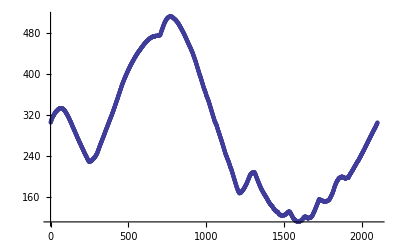

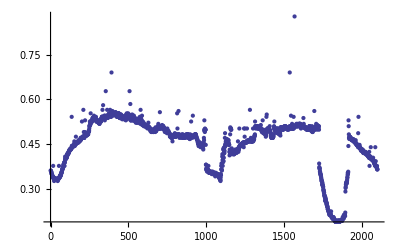

```mathematica
ListPlot[s⟦All,1⟧]
ListPlot[s⟦All,2⟧]
(*This is the depth information*)
ListPlot[s⟦All,3⟧]
```

```mathematica
ListPointPlot3D[Table[{s⟦i,1⟧,s⟦i,2⟧,s⟦i,3⟧},{i,1,Length[s]}]]
```

-Graphics3D-